```mathematica
(*Mathematica*)
```

```mathematica
(*https://oeis.org/A143472*)
```

```mathematica
CoefficientList[Series[1/(1-x^3-x^5-x^7+x^10),{x,0,50}],x]
```

{1,0,0,1,0,1,1,1,2,1,2,3,3,4,5,6,7,9,11,14,17,20,26,31,38,48,58,72,88,108,134,164,202,249,306,376,463,570,701,863,1061,1306,1607,1976,2433,2993,3682,4531,5574,6859,8439}

```mathematica
g[x_]=(1-x^3-x^5-x^7+x^10)
```

1-x^3-x^5-x^7+x^10

```mathematica
f[x_]=ExpandAll[x^10*g[1/x]]
```

1-x^3-x^5-x^7+x^10

```mathematica
v=x/.NSolve[f[x]==0,x]
```

{-0.848247-0.5296 ⅈ,-0.848247+0.5296 ⅈ,-0.63842-0.769688 ⅈ,-0.63842+0.769688 ⅈ,-0.0999667-0.994991 ⅈ,-0.0999667+0.994991 ⅈ,0.565064-0.825047 ⅈ,0.565064+0.825047 ⅈ,0.812749,1.23039}

```mathematica
Abs[v]
```

{1.,1.,1.,1.,1.,1.,1.,1.,0.812749,1.23039}

```mathematica
ComplexListPlot[v,PlotStyle->Red,ImageSize->Medium]
```

```mathematica
(*end*)
```

```mathematica
(*Mathematica*)
```

```mathematica
dynamicNewtonPic[fIn_, {var_,varMin_,varMax_}, resolution_, bail_: 50] := Module[
	{f, n, limitInfo, color, colors, roots, preColors, step, limitData, 
	 r, xmin,xmax,ymin,ymax, z, pic},

	f = Function[var, fIn]; (* A very standard example *)
	n = Function[var, Evaluate[Simplify[var - f[var]/f'[var]]]];

	r = 0.01;
	limitInfo = With[{bailLoc = bail, rLoc = r, fLoc = f, nLoc = n},
	   Compile[{{z0, _Complex}},
		Module[{zz, cnt},
		 cnt = 0; zz = z0;
		 While[Abs[fLoc[zz]] > rLoc && cnt < bailLoc,
		  zz = nLoc[zz];
		  cnt = cnt + 1
		  ];
		 {zz, cnt}],
		RuntimeAttributes -> {Listable},
		Parallelization -> True,
		RuntimeOptions -> "Speed"
		]];

	xmin=Re[varMin];
	xmax=Re[varMax];
	ymin=Im[varMin];
	ymax=Im[varMax];
	step = Max[xmax-xmin,ymax-ymin]/(resolution+1);
	limitData = limitInfo[
	  ParallelTable[x + I*y, {y, ymax,ymin, -step}, {x, xmin,xmax, step}]];
	roots = z /. NSolve[f[z] == 0, z];
	preColors = List @@@ Table[ColorData[61, k], {k, 1, Length[roots]}];
	preColors = Append[preColors, {0.0, 0.0, 0.0}];
	color = With[{bailLoc = bail, rootsLoc = roots, preColorsLoc = preColors},
	   Compile[{{z, _Complex}, {cnt, _Complex}},
		Module[{arg, time, i},
		 arg = Arg[z];
		 time = Abs[cnt];
		 i = 1;
		 Scan[If[Abs[z - #] < 0.1, Return[i], i++] &, rootsLoc];
		 Abs[preColorsLoc[[i]]*(cnt/bailLoc)^(N[1/9])]
		 (* The exponent 0.2 adjusts the brightness of the image. *)]]
	];
	colors = Apply[color, limitData, {2}];
	pic = Graphics[Raster[colors,{{xmin,ymin},{xmax,ymax}}], 
		ImageSize -> 3/step,Frame->True];
	Panel[DynamicModule[{pt={0,0}},
		LocatorPane[Dynamic[pt],
			Show[{pic,
				Graphics[{Thick,Purple,Dynamic[Line[{Re[#],Im[#]}& /@
					NestWhileList[n,pt[[1]]+pt[[2]]*I,0.01<Abs[#]<10&,1,100]]]}]},
				PlotRange -> {{xmin,xmax},{ymin,ymax}},
				ImageSize -> resolution
			]
		]
	]]
];
```

```mathematica
(*https://oeis.org/A143472*)
```

```mathematica
g[x_]=(1-x^3-x^5-x^7+x^10)

f[x_]=ExpandAll[x^10*g[1/x]]
```

1-x^3-x^5-x^7+x^10

1-x^3-x^5-x^7+x^10

```mathematica
f10[x_]=x+f[x]/D[f[x],{x,1}]
```

x+(1-x^3-x^5-x^7+x^10)/(-3 x^2-5 x^4-7 x^6+10 x^9)

```mathematica
(*Preamplifaction of Newton effect experiment:*)
```

```mathematica
f1[x_]=D[f[x]^3,{x,1}]
```

3 (-3 x^2-5 x^4-7 x^6+10 x^9) (1-x^3-x^5-x^7+x^10)^2

```mathematica
g[x_]=x+f[x]^3/f1[x]
```

x+(1-x^3-x^5-x^7+x^10)/(3 (-3 x^2-5 x^4-7 x^6+10 x^9))

```mathematica
h[z_]=Together[ExpandAll[1/g[z]^3]]
```

(27 z^6 (-3-5 z^2-7 z^4+10 z^7)^3)/(1-30 z^3-48 z^5+300 z^6-66 z^7+960 z^8-1000 z^9+2181 z^10-4800 z^11+2112 z^12-16140 z^13+1452 z^14-28192 z^15+9300 z^16-35508 z^17+29760 z^18-23232 z^19+67611 z^20-10648 z^21+65472 z^22-28830 z^23+45012 z^24-46128 z^25-63426 z^27+29791 z^30)

```mathematica
Factor[Denominator[h[x]]]
```

(1-10 x^3-16 x^5-22 x^7+31 x^10)^3

```mathematica
v=x/.NSolve[(1-10 x^3-16 x^5-22 x^7+31 x^10)==0,x]
```

{-0.706853-0.598209 ⅈ,-0.706853+0.598209 ⅈ,-0.292276-0.390229 ⅈ,-0.292276+0.390229 ⅈ,-0.173392-0.746108 ⅈ,-0.173392+0.746108 ⅈ,0.41137-0.642585 ⅈ,0.41137+0.642585 ⅈ,0.420539,1.10176}

```mathematica
Table[Abs[v[[i]]],{i,Length[v]}]
```

{0.92601,0.92601,0.487549,0.487549,0.765991,0.765991,0.762981,0.762981,0.420539,1.10176}

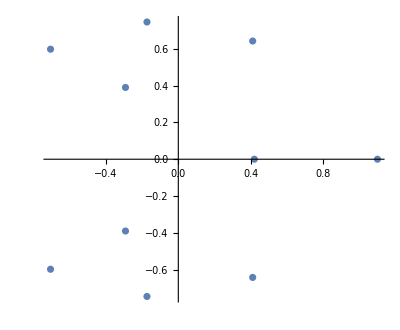

```mathematica
ComplexListPlot[v]
```

```mathematica
g[x_]=1-10 x^3-16 x^5-22 x^7+31 x^10
```

1-10 x^3-16 x^5-22 x^7+31 x^10

```mathematica
g[x_]=ExpandAll[x^10*g[1/x]]
```

31-22 x^3-16 x^5-10 x^7+x^10

```mathematica
gout=dynamicNewtonPic[f[x],{x,-2-2*I,2+2*I},2000];
```

```mathematica
Export["dynamicNewtonPic_new_Salem_Decic_10_A143472_PreAmp_exp4_2000res_lt9th.jpg",gout]
```

dynamicNewtonPic_new_Salem_Decic_10_A143472_PreAmp_exp4_2000res_lt9th.jpg

dynamicNewtonPic_new_Salem_Decic_10_A143472_PreAmp_exp4_2000res_lt9th.jpg

```mathematica
(*end*)
```

```mathematica
(*Mathematica*)
```

```mathematica
dynamicNewtonPic[fIn_, {var_,varMin_,varMax_}, resolution_, bail_: 50] := Module[
	{f, n, limitInfo, color, colors, roots, preColors, step, limitData, 
	 r, xmin,xmax,ymin,ymax, z, pic},

	f = Function[var, fIn]; (* A very standard example *)
	n = Function[var, Evaluate[Simplify[var - f[var]/f'[var]]]];

	r = 0.01;
	limitInfo = With[{bailLoc = bail, rLoc = r, fLoc = f, nLoc = n},
	   Compile[{{z0, _Complex}},
		Module[{zz, cnt},
		 cnt = 0; zz = z0;
		 While[Abs[fLoc[zz]] > rLoc && cnt < bailLoc,
		  zz = nLoc[zz];
		  cnt = cnt + 1
		  ];
		 {zz, cnt}],
		RuntimeAttributes -> {Listable},
		Parallelization -> True,
		RuntimeOptions -> "Speed"
		]];

	xmin=Re[varMin];
	xmax=Re[varMax];
	ymin=Im[varMin];
	ymax=Im[varMax];
	step = Max[xmax-xmin,ymax-ymin]/(resolution+1);
	limitData = limitInfo[
	  ParallelTable[x + I*y, {y, ymax,ymin, -step}, {x, xmin,xmax, step}]];
	roots = z /. NSolve[f[z] == 0, z];
	preColors = List @@@ Table[ColorData[61, k], {k, 1, Length[roots]}];
	preColors = Append[preColors, {0.0, 0.0, 0.0}];
	color = With[{bailLoc = bail, rootsLoc = roots, preColorsLoc = preColors},
	   Compile[{{z, _Complex}, {cnt, _Complex}},
		Module[{arg, time, i},
		 arg = Arg[z];
		 time = Abs[cnt];
		 i = 1;
		 Scan[If[Abs[z - #] < 0.1, Return[i], i++] &, rootsLoc];
		 Abs[preColorsLoc[[i]]*(cnt/bailLoc)^(N[1/9])]
		 (* The exponent 0.2 adjusts the brightness of the image. *)]]
	];
	colors = Apply[color, limitData, {2}];
	pic = Graphics[Raster[colors,{{xmin,ymin},{xmax,ymax}}], 
		ImageSize -> 3/step,Frame->True];
	Panel[DynamicModule[{pt={0,0}},
		LocatorPane[Dynamic[pt],
			Show[{pic,
				Graphics[{Thick,Purple,Dynamic[Line[{Re[#],Im[#]}& /@
					NestWhileList[n,pt[[1]]+pt[[2]]*I,0.01<Abs[#]<10&,1,100]]]}]},
				PlotRange -> {{xmin,xmax},{ymin,ymax}},
				ImageSize -> resolution
			]
		]
	]]
];
```

```mathematica
(*https://oeis.org/A143472*)
```

```mathematica
g[x_]=(1-x^3-x^5-x^7+x^10)

f[x_]=ExpandAll[x^10*g[1/x]]
```

1-x^3-x^5-x^7+x^10

```mathematica
f10[x_]=x+f[x]/D[f[x],{x,1}]
```

x+(1-x^3-x^5-x^7+x^10)/(-3 x^2-5 x^4-7 x^6+10 x^9)

```mathematica
(*Preamplifaction of Newton effect experiment:*)
```

```mathematica
f1[x_]=D[f[x]^3,{x,1}]
```

3 (-3 x^2-5 x^4-7 x^6+10 x^9) (1-x^3-x^5-x^7+x^10)^2

```mathematica
g[x_]=x+f[x]^3/f1[x]
```

x+(1-x^3-x^5-x^7+x^10)/(3 (-3 x^2-5 x^4-7 x^6+10 x^9))

```mathematica
h[z_]=Together[ExpandAll[1/g[z]^3]]
```

(27 z^6 (-3-5 z^2-7 z^4+10 z^7)^3)/(1-30 z^3-48 z^5+300 z^6-66 z^7+960 z^8-1000 z^9+2181 z^10-4800 z^11+2112 z^12-16140 z^13+1452 z^14-28192 z^15+9300 z^16-35508 z^17+29760 z^18-23232 z^19+67611 z^20-10648 z^21+65472 z^22-28830 z^23+45012 z^24-46128 z^25-63426 z^27+29791 z^30)

```mathematica
Factor[Denominator[h[x]]]
```

(1-10 x^3-16 x^5-22 x^7+31 x^10)^3

```mathematica
v=x/.NSolve[(1-10 x^3-16 x^5-22 x^7+31 x^10)==0,x]
```

{-0.706853-0.598209 ⅈ,-0.706853+0.598209 ⅈ,-0.292276-0.390229 ⅈ,-0.292276+0.390229 ⅈ,-0.173392-0.746108 ⅈ,-0.173392+0.746108 ⅈ,0.41137-0.642585 ⅈ,0.41137+0.642585 ⅈ,0.420539,1.10176}

```mathematica
Table[Abs[v[[i]]],{i,Length[v]}]
```

{0.92601,0.92601,0.487549,0.487549,0.765991,0.765991,0.762981,0.762981,0.420539,1.10176}

```mathematica
ComplexListPlot[v]
```

-Graphics-

```mathematica
g[x_]=1-10 x^3-16 x^5-22 x^7+31 x^10
```

1-10 x^3-16 x^5-22 x^7+31 x^10

```mathematica
g[x_]=ExpandAll[x^10*g[1/x]]
```

31-22 x^3-16 x^5-10 x^7+x^10

```mathematica
gout=dynamicNewtonPic[g[x],{x,-2-2*I,2+2*I},2000];
```

```mathematica
Export["dynamicNewtonPic_new_Salem_Decic_10_toral_Inverse_A143472_PreAmp_exp4_2000res_lt9th.jpg",gout]
```

dynamicNewtonPic_new_Salem_Decic_10_toral_Inverse_A143472_PreAmp_exp4_2000res_lt9th.jpg

```mathematica
(*end*)
```